```mathematica
v=25*50*2.2
```

2750.

```mathematica
vmax=(25+0.01)*(50+0.01)*(2.2+0.01)
```

2764.16

```mathematica
vmin=(25-0.01)*(50-0.01)*(2.2-0.01)
```

2735.86

```mathematica
ag=Max[Abs[vmax-v],Abs[vmin-v]]
```

14.1577

```mathematica
rg=ag/v
```

0.00514826

```mathematica
cv={{8,78},{11,85},{13,97},{19,89},{22,81}}
```

{{8,78},{11,85},{13,97},{19,89},{22,81}}

```mathematica
lagranz[cv_,x_]:=Module[{},
m=Length[cv];
w=1;
pol=0;
Do[
w=w*(x-cv[[i,1]]),
{i,1,m}];
Do[
wi=w/(x-cv[[i,1]]);
pol=pol+cv[[i,2]]*wi/(wi/.x->cv[[i,1]]),
{i,1,m}];
pol
]
```

```mathematica
polinom[x_]=lagranz[cv,x]
```

13/385 (-22+x) (-19+x) (-13+x) (-11+x)-85/528 (-22+x) (-19+x) (-13+x) (-8+x)+97/540 (-22+x) (-19+x) (-11+x) (-8+x)-(89 (-22+x) (-13+x) (-11+x) (-8+x))/1584+3/154 (-19+x) (-13+x) (-11+x) (-8+x)

```mathematica
apx=polinom[14]//N
```

101.087

```mathematica
ag=Abs[apx-92]
```

9.08658

```mathematica
rg=ag/92
```

0.0987672

```mathematica
cv={{1984-1984,8.54},{1988-1984,8.72},{1996-1984,8.50},{2004-1984,8.59},{2008-1984,8.34},{2016-1984,8.31}}
```

{{0,8.54},{4,8.72},{12,8.5},{20,8.59},{24,8.34},{32,8.31}}

```mathematica
pol[t_]=Fit[cv,{1,t},t]
```

8.64815-0.00966192 t

```mathematica
pol[16]
```

8.49356

```mathematica
ag=Abs[pol[16]-8.55]
```

0.0564413

```mathematica
linearniSplajn[cv_,x0_]:=Module[{},
m=Length[cv];
Do[
If[cv[[i,1]]<=x0<=cv[[i+1,1]],
res=cv[[i,2]]+(cv[[i+1,2]]-cv[[i,2]])/(cv[[i+1,1]]-cv[[i,1]])(x0-cv[[i,1]])
],
{i,1,m-1}];
res
]
```

```mathematica
gr1=ListPlot[cv];
gr2=Plot[linearniSplajn[cv,x],{x,0,32},PlotStyle->Red];
```

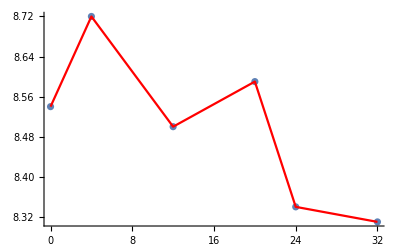

```mathematica
Show[gr1,gr2,PlotRange->All]
```